# Advanced 3D Printing with MeshRegions

Math 213 - Math with Mathematica
Christopher Hanusa

## Overview

Today we will work with MeshRegion objects, the native object that Mathematica uses when exporting for 3D Printing.  Understanding it will allow you to better know what is and is not exportable as a 3D model.  For example, when you import an STL file, your object is a MeshRegion Object.

```mathematica
?MeshRegion
```

A good list of related commands is given in this Mesh-Based Geometric Regions guide.

## Resizing MeshRegions

When you are finalizing your Shapeways object, you will have a 3D rendering of your object that you created using coordinates with dimensions determined by mathematical units.  When you upload to Shapeways, your model will need to be scaled to be in either millimeters or in inches.  Furthermore, you may need to change this to adjust the cost of your model.  There is an easy way to change the size of a model when it is a MeshRegion object---use RegionResize.  If you only use one parameter as the second input, it will scale the object to have first coordinate equal to that input.  If you specify a list of parameters, it will scale the object to fit into the given box, not respecting the ratios between side lengths.

```mathematica
mesh=Import[Export[NotebookDirectory[]<>"SnubCube.stl",PolyhedronData["SnubCube","Polyhedron"]]]
```

Here we use RegionBounds to see that the standard size of this object is 2.29 units wide.

```mathematica
RegionBounds[mesh]
```

If we instead want it to be 2 units wide, we can do this:

```mathematica
newmesh=RegionResize[mesh, 2]
```

```mathematica
RegionBounds[newmesh]
```

If we want to skew it differently in each direction, we can do this:

```mathematica
skewmesh=RegionResize[mesh, {2,1,10}]
```

```mathematica
RegionBounds[skewmesh]
```

## Comprehension Question

### 1. Use this technique to create an ellipsoid that has dimensions 2”x3”x4”.

## DiscretizeGraphics

In order to turn a 2D or 3D Graphics object into a MeshRegion object without exporting then importing, use DiscretizeGraphics.  Applying this function changes the object from its ideal mathematical representation into a shape built of points/lines/polygons/tetrahedra/simplices.

Here is an example of changing an oval into an approximating polygon.

```mathematica
oval=Graphics[Disk[{0,0},{6,4}]]
```

```mathematica
ovalmesh=DiscretizeGraphics[oval]
```

And here is how you can discretize a sphere:

```mathematica
shape3d=Graphics3D[Sphere[{0,0,0},.1]]
```

```mathematica
ball=DiscretizeGraphics[shape3d]
```

## Region Operations

RegionIntersection, RegionUnion, and RegionDifference are used to intersect, merge, or subtract two regions.  They work well in 2D, but RegionIntersection and RegionDifference do not work well in 3D.

### 2D Examples

```mathematica
ovalmesh=DiscretizeGraphics[Graphics[Disk[{0,0},{6,4}]]]
trianglemesh=DiscretizeGraphics[Graphics[Polygon[{{-2,-7},{-2,7},{4,0}}]]]
squaremesh=DiscretizeGraphics[Graphics[Polygon[{{0,0},{0,1},{1,1},{1,0}}]]]
```

The union of the oval and the triangle:

```mathematica
RegionUnion[ovalmesh,trianglemesh]
```

The intersection of the oval and the triangle:

```mathematica
RegionIntersection[ovalmesh,trianglemesh]
```

The oval with the square removed:

```mathematica
RegionDifference[ovalmesh,squaremesh]
```

### 3D Examples

```mathematica
ball=DiscretizeGraphics[Graphics3D[Sphere[{0,0,0},1]]]
cube=DiscretizeGraphics[Graphics3D[Cuboid[{0,0,0},{1,1,1}]]]
tetrahedron=DiscretizeGraphics[PolyhedronData["Tetrahedron","Polyhedron"]]
```

Here you can see that you can make the union of two 3D meshes, but the intersection and the difference don’t  work

```mathematica
{RegionUnion[ball,cube],RegionUnion[tetrahedron,cube]}
RegionIntersection[ball,cube]
RegionDifference[ball,cube]
RegionDifference[ball,tetrahedron]
```

## Comprehension Question

### 2. The Cube and the Octahedron are two dual polyhedra. Use PolyhedronData and DiscretizeGraphics to import both of them as meshes. Then create the union of these two shapes so that you can see all 6 vertices of the octahedron poking through the faces of the cube, and all 8 vertices of the cube poking through the faces of the octahedron. You may wish to use RegionResize to change the relative sizes of these shapes.

## Images

You can also discretize images:

### Drag and drop your image here.

```mathematica
flower=-Graphics-;
```

### Code to discretize.

```mathematica
image=ImageMesh[ColorNegate[flower]]
```

## Text

And also discretize words in whatever font your computer has installed.

```mathematica
word=Text[Style["word",Bold,FontFamily->"Bauhaus 93",FontSize->50]]
```

```mathematica
text=DiscretizeGraphics[word,_Text]
```

## Example: Creating a name plate

Here we create a plaque that has a raised image on it.  We first need to discretize the shape of the background:

```mathematica
shape=DiscretizeGraphics[Graphics[Rectangle[{0,0},{2,1}]]];
```

And then we discretize the image.

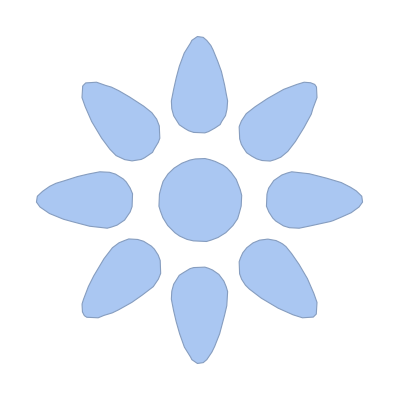
```mathematica
image=-Graphics-;
```

Here we resize the background shape and the image so that they fit inside one another.
We also make sure that these resized meshes are translated to have the same center.  (Use a TransformedRegion command involving a TranslationTransform)
They are showed together to make sure that the sizes and alignment are correct.

```mathematica
resizedShape=RegionResize[shape,2.5];
resizedImage=RegionResize[image,1];
translatedShape=TransformedRegion[resizedShape,TranslationTransform[-Map[Mean,RegionBounds[resizedShape]]]];
translatedImage=TransformedRegion[resizedImage,TranslationTransform[-Map[Mean,RegionBounds[resizedImage]]]];
Show[translatedShape,translatedImage]
```

Now we need to remove the image to create the flat layer that is the middle of the plate.

```mathematica
background=translatedShape;
foreground=translatedImage;
middle=BoundaryDiscretizeRegion[RegionDifference[background,foreground]]
```

The RegionBoundary command takes the boundary lines of the 2D shape:

```mathematica
outerboundary=RegionBoundary[background]
innerboundary=RegionBoundary[foreground]
```

Last, we use the RegionProduct command to add three-dimensionality to the nameplate.

```mathematica
nameplate=Show[{
RegionProduct[background,Point[{{0.}}]],
RegionProduct[outerboundary,Line[{{0.},{.1}}]],
RegionProduct[middle,Point[{{.1}}]],
RegionProduct[innerboundary,Line[{{.1},{.2}}]],
RegionProduct[foreground,Point[{{.2}}]]
}]
```

```mathematica
Export[NotebookDirectory[]<>"nameplate.stl",nameplate]
```

## Comprehension Question

### 3. Create a name plate with your name on it. Change the background shape to be a different shape than a rectangle.

## Challenge Question

### 4. Use a Table Command and TransformedRegion/TranslationTransform to create an army of hundreds of octahedra and cubes.

## Accessing Parts of a MeshRegion Object

Use MeshCoordinates and MeshPrimitives to get information out of a MeshRegion Object.  MeshCoordinates will extract the coordinates of the mesh

```mathematica
coords=MeshCoordinates[ball];
```

```mathematica
first10=Take[coords,10]
```

```mathematica
Graphics3D[Map[Point,coords]]
```

Use MeshPrimitives will extract other parts of the object, like its edges or polygonal faces.

```mathematica
edges=MeshPrimitives[ball,1];  (* edges have dimension 1 *)
```

```mathematica
first10=Take[edges,10]
```

```mathematica
Graphics3D[edges]
```

```mathematica
faces=MeshPrimitives[ball,2];  (* faces have dimension 2 *)
```

```mathematica
first10=Take[faces,10]
```

```mathematica
Graphics3D[faces]
```

## Comprehension Question

### Extract the edges of one of the models you exported from the last tutorial. Then use the Map function to create a wireframe of the object like this for the sphere:

```mathematica
Graphics3D@Map[Tube,edges[[All,1]]]
```

## Example: Costa Rica Pendant

This is an example in which the geography of Costa Rica is transformed into a polygon, and then given some thickness by adding in rectangles along the boundary to connect two polygonal sheets distance 0.25 apart.

```mathematica
CREdges=CountryData[Entity["Country","CostaRica"],"Polygon"][[1,1,1]];
```

```mathematica
Graphics3D[{Polygon[Map[Prepend[#,0]&,CREdges]],Polygon[Map[Prepend[#,0.25]&,CREdges]]}]
```

```mathematica
Graphics3D[{Table[Polygon[{
Prepend[CREdges[[i]],0],
Prepend[CREdges[[Mod[i+1,Length[CREdges],1]]],0],
Prepend[CREdges[[Mod[i+1,Length[CREdges],1]]],0.25],
Prepend[CREdges[[i]],0.25]}],{i,Length[CREdges]}]}]
```

## Other 3D modeling commands: BSplineSurface

If you have (x_i,y_i,z_i) control points and you’d like a surface that is a smooth function z=f(x,y), then use BSplineSurface

```mathematica
cpts=Table[{i,j,RandomReal[{-1,1}]},{i,5},{j,5}];
```

```mathematica
b=Graphics3D[BSplineSurface[cpts]]
```

```mathematica
Show[Graphics3D[{PointSize[Medium],Red,Map[Point,cpts],Gray,Line[cpts],Line[Transpose[cpts]]}],b]
```

This is from the Wolfram Demonstration: “Designing a Car Body with Splines” available here:
http://demonstrations.wolfram.com/DesigningACarBodyWithSplines/

```mathematica
Manipulate[
Graphics3D[{
color,Specularity[White,50],
BSplineSurface[carbody,SplineDegree->Floor[degrees]],
If[mesh,
{Dashed,Blue,Line[carbody],Line[Transpose[carbody]],Red,PointSize[Medium],Point/@carbody},{}]},
Boxed->False,Lighting->"Neutral",RotationAction->"Clip",ViewPoint->{-2,-2,2}],
Row[{Control[{{degrees,{1,1}},{1,1},{14,7},ImageSize->{140,70}}],Dynamic[Floor[degrees]]},Spacer[10]],
Row[{Control[{color,ColorData["HTML","GoldenRod"]}],Control[{mesh,{False,True}}]},Spacer[10]],
Initialization:>(carbody={
{{-.2,-2.25,0},{-.2,-2.25,0},{-.2,-2,0},{-.2,0,0},{-.2,2,0},{-.2,2.25,0},{-.2,2.25,0}},
{{0,-2.25,0},{0,-2.25,1.75},{0,-2,1.75},{0,0,1.75},{0,2,1.75},{0,2.25,1.75},{0,2.25,0}},
{{1,-2.25,0},{1,-2.25,1.75},{1,-2,1.75},{1,0,1.75},{1,2,1.75},{1,2.25,1.75},{1,2.25,0}},
{{1.01,-2.25,1.5},{1.01,-2.25,1.75},{1.01,-2,1.75},{1.01,0,1.75},{1.01,2,1.75},{1.01,2.25,1.75},{1.01,2.25,1.5}},
{{2.99,-2.25,1.5},{2.99,-2.25,1.75},{2.99,-2,1.75},{2.99,0,1.75},{2.99,2,1.75},{2.99,2.25,1.75},{2.99,2.25,1.5}},
{{3,-2.25,0},{3,-2.25,1.75},{3,-2,1.75},{3,0,1.75},{3,2,1.75},{3,2.25,1.75},{3,2.25,0}},
{{4,-2.25,0},{4,-2.25,1.75},{4,-2,1.75},{4,0,1.75},{4,2,1.75},{4,2.25,1.75},{4,2.25,0}},
{{5,-2.25,0},{5,-2.25,1.75},{5,-2,3.5},{5,0,3.5},{5,2,3.5},{5,2.25,1.75},{5,2.25,0}},
{{8,-2.25,0},{8,-2.25,1.75},{8,-2,3.5},{8,0,3.5},{8,2,3.5},{8,2.25,1.75},{8,2.25,0}},
{{8.01,-2.25,1.5},{8.01,-2.25,1.75},{8.01,-2,3.5},{8.01,0,3.5},{8.01,2,3.5},{8.01,2.25,1.75},{8.01,2.25,1.5}},
{{9,-2.25,1.5},{9,-2.25,2},{9,-2,2},{9,0,2},{9,2,2},{9,2.25,2},{9,2.25,1.5}},
{{9.99,-2.25,1.5},{9.99,-2.25,2},{9.99,-2,2},{9.99,0,2},{9.99,2,2},{9.99,2.25,2},{9.99,2.25,1.5}},
{{10,-2.25,0},{10,-2.25,2},{10,-2,2},{10,0,2},{10,2,2},{10,2.25,2},{10,2.25,0}},
{{11,-2.25,0},{11,-2.25,2},{11,-2,2},{11,0,2},{11,2,2},{11,2.25,2},{11,2.25,0}},
{{11.01,-2.25,0},{11.01,-2.25,0},{11.01,-2,0},{11.01,0,0},{11.01,2,0},{11.01,2.25,0},{11.01,2.25,0}}
})]
```

## Example: ParametricPlot3D for a pendant

Here is the code I used to create my Polaris Pendant, which is made up of parabolas.  You can see that I first created a 2D version of the design, so that I could determine the correct functions that I wanted to include.

```mathematica
Show[{Graphics[Circle[{1.25,1.25},.75]],
ParametricPlot[{{t,1-(t-1.25)^2},{t,1.5+(t-1.25)^2}},{t,0.7201166105600068,1.7798833894399924}],
ParametricPlot[{{t,1.15-1/2(t-1.25)^2},{t,1.35+1/2(t-1.25)^2}},{t,0.5753270351715947,1.924672964828405}],
ParametricPlot[{{1-(u-1.25)^2,u},{1.5+(u-1.25)^2,u}},{u,0.7201166105600068,1.7798833894399924}],
ParametricPlot[{{1.15-1/2(u-1.25)^2,u},{1.35+1/2(u-1.25)^2,u}},{u,0.5753270351715947,1.924672964828405}]
},PlotRange->{{.48,2.02},{.48,2.02}}]
```

Then I converted each of the 2D ParametricPlot functions to 3D ParametricPlot3D functions.

```mathematica
pendant=Show[{
ParametricPlot3D[{.75Cos[t]+1.25,.75Sin[t]+1.25,0},{t,0,2Pi},PlotStyle->Tube[.04,PlotPoints->50]],
ParametricPlot3D[{{t,1-(t-1.25)^2,0},{t,1.5+(t-1.25)^2,0}},{t,0.7201166105600068,1.7798833894399924},PlotStyle->Tube[.03,PlotPoints->50]],
ParametricPlot3D[{{t,1.15-1/2(t-1.25)^2,0},{t,1.35+1/2(t-1.25)^2,0}},{t,0.5753270351715947,1.924672964828405},PlotStyle->Tube[.03,PlotPoints->50]],
ParametricPlot3D[{{1-(u-1.25)^2,u,0},{1.5+(u-1.25)^2,u,0}},{u,0.7201166105600068,1.7798833894399924},PlotStyle->Tube[.03,PlotPoints->50]],
ParametricPlot3D[{{1.15-1/2(u-1.25)^2,u,0},{1.35+1/2(u-1.25)^2,u,0}},{u,0.5753270351715947,1.924672964828405},PlotStyle->Tube[.03,PlotPoints->50]]
},PlotRange->{{.48,2.02},{.48,2.02},{-.2,.2}}]
```